```mathematica
ClearAll["Global`*"]
```

# -Graphics-

Plot options and export function

```mathematica
figpath[filename_]:=StringTemplate["/Users/basavyr/Documents/Work/PhD/phdthesis/Chapters/Figures/``.pdf"][filename];
export[object_,name_]:=Export[figpath[name],object/. {EdgeForm[],r_?(MemberQ[{RGBColor,Hue,CMYKColor,GrayLevel},Head[#]]&),i___}:>{EdgeForm[r],r,i},ImageResolution->1500];
```

```mathematica
j0=11/2;
theta0=70*π/180;
j1=j0*Cos[theta0];
j2=j0*Sin[theta0];
moi1=10;
moi2=40;
moi3=20;
A1Const=1/(2*moi1);
A2Const=1/(2*moi2);
A3Const=1/(2*moi3);
```

```mathematica
x1[I_,theta_,phi_]:=I*Sin[theta]*Sin[phi];
x2[I_,theta_,phi_]:=I*Cos[theta];
x3[I_,theta_,phi_]:=I*Sin[theta]*Cos[phi];
A[I_]:=A2Const*(1-j2/I)-A1Const;
u[I_]:=(A3Const-A1Const)/A[I];
v0[I_]:=(-A1Const*j1)/A[I];
Hprime[I_,theta_,phi_]:=x2[I,theta,phi]^2+u[I]*x3[I,theta,phi]^2+2*v0[I]*x1[I,theta,phi];
```

```mathematica
(* Trick for custom ticks *)
(* source: https://mathematica.stackexchange.com/questions/190490/add-minor-ticks-to-custom-ticks?noredirect=1&lq=1 *)
tickFuncText[x_,y_]:=Join[{#,#,{.03,0}}&/@Subdivide[y,x],{#," ",{.01,0}}&/@Subdivide[##,5*x]]&;
tickFuncMute[x_,y_]:=Join[{#," ",{.03,0}}&/@Subdivide[y,x],{#," ",{.01,0}}&/@Subdivide[##,5*x]]&;
```

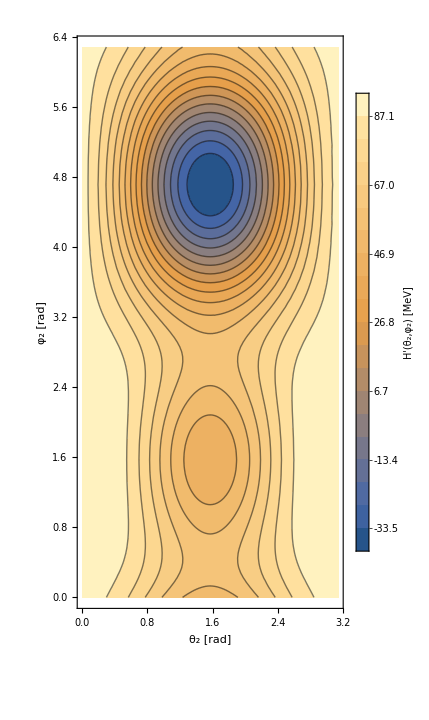

```mathematica
cp[I_]:=ContourPlot[Hprime[I,theta,phi],{theta,0,π},{phi,0,2π},AspectRatio->Automatic,Contours->16,Frame->True,FrameStyle->Directive[Black,Thick],PlotRangePadding->None,LabelStyle->{19,Black,FontFamily->"Latin Modern Roman"},PlotLegends->BarLegend[Automatic,19,LegendLabel->Style["H'(θ_2,φ_2)\n[MeV]",Italic]],ImageSize->Medium,FrameLabel->{"θ_2 [rad]","φ_2 [rad]"},FrameTicks->{{Automatic,Automatic},{tickFuncText[3,3],tickFuncMute[3,3]}}];
Show[cp[19/2]]
export[cp[19/2],"New-Boson-Classical-H-2axis-quantization"];
```